```mathematica
g=9.8; (*grav. constant*)
l=0.5; (*length of pendulum*)
c = 3 10^8;
m = 1;
vt = Sqrt[m g/c];

V = 30;
th = 50 Pi/180; (*converted to radians*)

sol = 
With[{vt=50},
NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),
{x[0]==0, y[0]==2},{x'[0]==V Cos[th],y'[0]==V Sin[th]}},{x,y},{t,0,200}]];
```

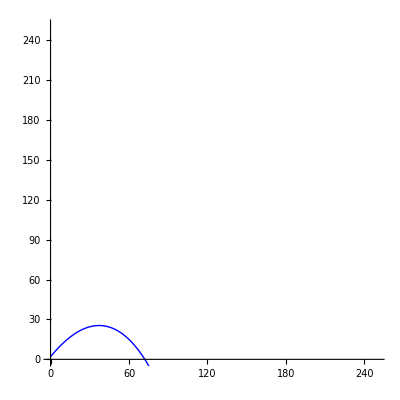

```mathematica
myplot1 = ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,200},PlotStyle-> RGBColor[0,0,1],PlotRange-> {0,250}];
Show[myplot1]
```

```mathematica
Manipulate[
Module[
{sol =NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),
{x[0]==0, y[0]==y0},{x'[0]==V Cos[th],y'[0]==V Sin[th]}},{x,y},{t,0,200}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{V Cos[th]t,y0 + V Sin[th]t-0.5g t^2}},{t,0,tf},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,150},{0,150}},ImageSize->{500,300}]],
{{y0,0,"initial height (m)"},0,100,Appearance->"Labeled"},
{{V,10,"initial velocity (m/s)"},10,200,Appearance->"Labeled"},
{{vt,10,"terminal velocity (m/s)"},10,200,Appearance->"Labeled"},
{{th,0.1,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{tf,0.01,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Module[
{sol =With[{vt = Sqrt[2 m 9.8/(0.5 1.29 A)]},
NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),
{x[0]==0, y[0]==2},{x'[0]==V Cos[th],y'[0]==V Sin[th]}},{x,y},{t,0,200}]]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{V Cos[th]t,y0 + V Sin[th]t-0.5g t^2}},{t,0,tf},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,150},{0,150}},ImageSize->{500,300}]],
{{A,0.001,"Area (m^2)"},0.001,1,Appearance->"Labeled"},
{{m,0.01,"mass (kg)"},0.01,3,Appearance->"Labeled"},
{{y0,0,"initial height (m)"},0,3,Appearance->"Labeled"},
{{V,10,"initial velocity (m/s)"},10,200,Appearance->"Labeled"},
{{th,0.1,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{tf,0.01,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```

```mathematica
data = 
{{ ,HumanCannonball,Golfball,Baseball},
{ initial speed,123 ,456  ,789  },
{ initial angle,123 ,456  , 789 }
};

Grid[data, Alignment->Left, Spacings->{2,1}, Frame->All, ItemStyle->"Text"]
```

| HumanCannonball | Golfball | Baseball
initial speed | 123 | 456 | 789
angle initial | 123 | 456 | 789